## 2 level Atoms (or 4 level atoms with Δ_1=Δ_2=Δ )

### Analytical Results for τ_m<<τ

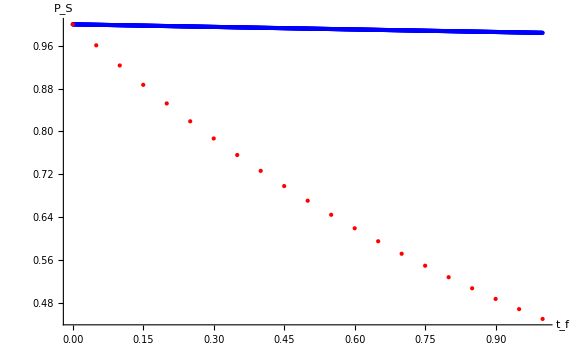

```mathematica
Psuccess[Δ_,τ_,t_]:=ⅇ^(-Δ^2 τ t);

IntervalSize1=0.001;
IntervalSize2=0.05;

plot[τ_]:=DiscretePlot[Psuccess[4,τ,t],{t,0,1,τ},AxesLabel->{Style[Subscript[t, f],30,Black],Style[Subscript[P, S],30,Black]},LabelStyle->Large,ImageSize->Large,PlotRange->{0,1},PlotStyle->{τ,IntervalUP Blue+τ,IntervalLOW Red, PointSize
[Large]},LabelStyle-> Large,Filling->None];


Print[Show[{plot[ IntervalSize1],plot[IntervalSize2]},PlotRange-> All]];
```